```mathematica
RiemannBar[box:{{x0_,x1_},{y0_,y1_}},{x_,y_},_]:=Block[{area=(y1+y0) (x1-x0)},Sow[area];
{(*ChartElementData["Rectangle"][box,{},{}],*)
{Opacity[0.5],Blue,EdgeForm[Thickness[Medium]],Rectangle[{x0,y0},{x1,y1}]},
{Opacity[1],Black,Point[{x,y}]},{Opacity[1],Black,Text[Rotate[NumberForm[area,{Infinity,2}],Pi/2],Mean/@box]}}]
RiemannPlot[f_,{x_,x0_,x1_,n_},opts___]:=Block[{plot,areas,extent,points,curve,dx=(x1-x0)/n,maxy,miny},extent=OptionValue[Flatten[{opts}],ExtentSize];
points=Switch[extent,Full,Range[x0+dx/2,x1-dx/2,dx],Left,Range[x0+dx,x1,dx],Right,Range[x0,x1-dx,dx]];
maxy=Max[Max[Map[f/.x->#&,points]],0];
miny=Min[Min[Map[f/.x->#&,points]],0];
{plot,areas}=Reap[DiscretePlot[f,Evaluate@{x,points},opts,ImageSize->275,ExtentElementFunction->RiemannBar,FillingStyle->Opacity[0.5],PlotStyle->PointSize[Medium],PlotRange->{miny,maxy}]];
Show[plot,Plot[f,{x,x0,x1},PlotStyle->{Thick,Red}],PlotLabel->Row[{"Estimated Area: ",Chop@Total[Flatten@areas],Spacer[10],"Actual Area: ",Chop@NIntegrate[f,{x,x0,x1}]}],Frame->True,PlotRange->All,Axes->{True,False}]]
Off[NIntegrate::ncvb]
Off[NIntegrate::slwcon]
```

```mathematica
RiemannPlot[x^2,{x,0,5,5}, ExtentSize->Full]
```

```mathematica
RiemannPlot[x^2,{x,-1,1,4}, ExtentSize->Full]
```

```mathematica
RiemannPlot[x^2,{x,0,5,5},ExtentSize->Left]
```

```mathematica
RiemannPlot[x^2,{x,0,5,5},ExtentSize->Right]
```

```mathematica
RiemannPlot[Sin[x],{x,0,π,3},ExtentSize->Full]
```

```mathematica
RiemannPlot[Sin[x],{x,0,π,6},ExtentSize->Full]
```

```mathematica
RiemannPlot[Sin[x],{x,0,π,10},ExtentSize->Full]
```

```mathematica
RiemannPlot[Sin[x],{x,0,π,100},ExtentSize->Full]
```

```mathematica
RiemannPlot[2x+3,{x,1,4,3},ExtentSize->Right]
```

```mathematica
RiemannPlot[1-t,{t,0,3,6},ExtentSize->Right]
```

```mathematica
f[x_]:=1+2Sin[2x]
F[x_]:=Evaluate[Integrate[f[t],{t,0,x}]]
```

```mathematica
a=0; b=4;
Manipulate[
Row[{
Show[Plot[f[t],{t,a,b},
PlotLabel-> Row[{"x=",x,"  Area under graph: ",NumberForm[NIntegrate[f[t],{t,0,x}],{5,2}]}],
PlotRange->{-1.1,3.1}, ImageSize->Medium],
If[x>0,Plot[f[t],{t,a,x},Filling->0],{}]],
Show[Plot[F[x],{x,a,b},ImageSize->Medium, PlotLabel->"Accumulation Function"], Graphics[{PointSize[Large],Point[{x,F[x]}]}]]}]
,{{x,1},0,4},ControlPlacement->Top]
```

```mathematica
a=0; b=4;
Manipulate[
Show[Plot[f[t],{t,a,b},
PlotLabel-> Row[{"x=",x,"  h=",h,"  Orange Area: ",NumberForm[NIntegrate[f[t],{t,x,x+h}],3], "  Divided by h: ",NumberForm[NIntegrate[f[t],{t,x,x+h}]/h,{5,2}]}],
PlotRange->{-1.1,3.1}, ImageSize->Medium],
If[x>0,Plot[f[t],{t,a,x},Filling->0],{}],
Plot[f[t],{t,x,x+h},Filling->0, FillingStyle->Directive[Opacity[0.5],Orange]]]
,{{x,1},0,4},{{h,0.1},0.001,0.1},ControlPlacement->Top]
```

```mathematica
(*Class 13 -- Logarithms*)
```

```mathematica
Manipulate[
Show[Plot[1/t,{t,-3,10},
PlotLabel-> Row[{"x=",x,"  Value: ",If[x>0,NumberForm[Log[x],3],"?"]}],
PlotRange->{-1.1,3.1}, ImageSize->Medium],
If[x!=1,Plot[1/t,{t,1,x},Filling->0],{}],Graphics[Line[{{1,0},{1,1}}]]]
,{{x,1},-3,10},ControlPlacement->Top]
```

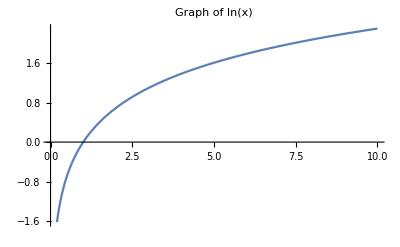

```mathematica
Plot[Log[t],{t,0,10},PlotLabel->"Graph of ln(x)"]
```

```mathematica
Plot[1/x,{x,-10,10}, PlotLabel->"Graph of 1/x"]
```

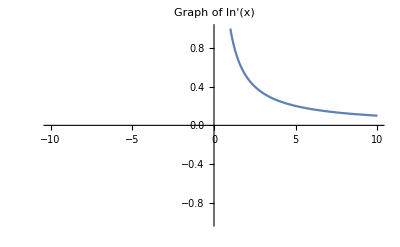

```mathematica
ln[x_]:=Evaluate[Piecewise[{{Integrate[1/t,{t,1,x}], x>0}, {Undefined, x<=0}}]]
Plot[ln'[x],{x,-10,10},PlotLabel->"Graph of ln'(x)", PlotRange -> {{-10,10},{-1,1}}]
```

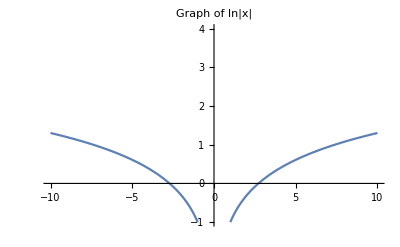

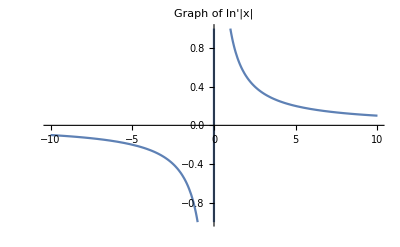

```mathematica
f[x_]:=Piecewise[{{ln[x], x>0}, {ln[-x], x<0}}]
Plot[f[x]-1,{x,-10,10},PlotLabel->"Graph of ln|x|", PlotRange -> {{-10,10},{-1,4}}]
Plot[f'[x],{x,-10,10},PlotLabel->"Graph of ln'|x|", PlotRange -> {{-10,10},{-1,1}}]
```

```mathematica
f[x_]:=3+Piecewise[{{ln[x], x>0}, {ln[-x], x<0}}]
Plot[f[x],{x,-10,10},PlotLabel->"Graph of 3+ln|x|", PlotRange -> {{-10,10},{-1,5}}]
Plot[f'[x],{x,-10,10},PlotLabel->"Graph of its derivative", PlotRange -> {{-10,10},{-1,1}}]
```

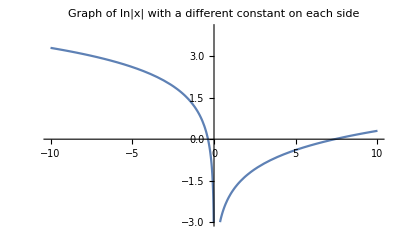

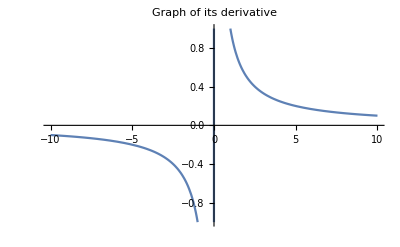

```mathematica
f[x_]:=Piecewise[{{ln[x]-2, x>0}, {ln[-x]+1, x<0}}]
Plot[f[x],{x,-10,10},PlotLabel->"Graph of ln|x| with a different constant on each side", PlotRange -> {{-10,10},{-3,4}}]
Plot[f'[x],{x,-10,10},PlotLabel->"Graph of its derivative", PlotRange -> {{-10,10},{-1,1}}]
```

```mathematica
Plot[-ln[Cos[x]],{x,-6,12},PlotLabel->"-ln(cos(x))", PlotRange->{-1,4}]
```

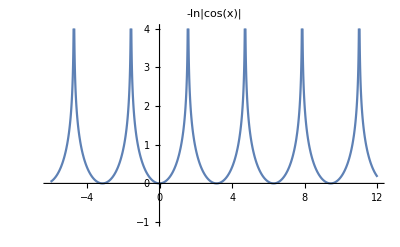

```mathematica
Plot[-ln[Abs[Cos[x]]],{x,-6,12},PlotLabel->"-ln|cos(x)|", PlotRange->{-1,4}]
```

```mathematica
randomconstants =<||>
randomconstant[x_]:=If[KeyExistsQ[randomconstants,Floor[x/π+1/2]],randomconstants[Floor[x/π+1/2]],randomconstants[Floor[x/π+1/2]]=RandomReal[{-3,3}]]
f[x_]:=-ln[Abs[Cos[x]]]+randomconstant[x]
```

<||>

<||>

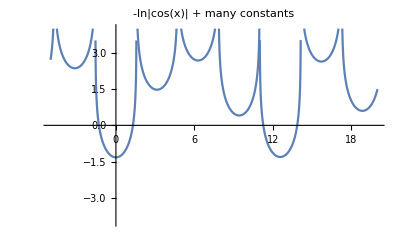

```mathematica
randomconstants=<||>
Plot[f[x],{x,-5,20},PlotLabel->"-ln|cos(x)| + many constants", PlotRange->{-4,4}]
```

```mathematica
Manipulate[
Show[Plot[Log[t],{t,0,10},
PlotLabel-> Row[{"x=",x,"  ln(x): ",If[x>0,NumberForm[Log[x],5],"?"]}],
PlotRange->{-1.1,3.1}, ImageSize->Medium],
Graphics[Line[{{x,0},{x,Log[x]}}]]]
,{{x,1},-3,10},ControlPlacement->Top]
```

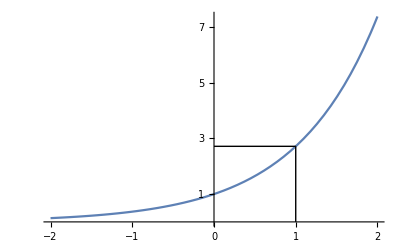

```mathematica
Show[Plot[Exp[t],{t,-2,2}, Ticks->{Automatic, Range[7]}],
Graphics[{Line[{{0,E},{1,E}}],Line[{{1,0},{1,E}}]}]]
```